```mathematica
$HistoryLength=0;
```

## Initialization

```mathematica
projectDirectory="~/Documents/unireps";
```

```mathematica
datasetsDirectory=FileNameJoin[{projectDirectory,"datasets"}];
outputsDirectory=FileNameJoin[{projectDirectory,"outputs"}];
knnDirectory=FileNameJoin[{projectDirectory,"knn"}];
```

```mathematica
mxDirectory=FileNameJoin[{projectDirectory,"mx"}];
```

```mathematica
figureDirectory=FileNameJoin[{ParentDirectory@NotebookDirectory[],"figures"}];
```

## Import k-NN

```mathematica
getDatasetName[{model_,dataset_,chat_:False}]:=
StringReplace[model,"/"->"__"]<>"---"<>dataset<>If[chat,"--chat",""]
```

```mathematica
getKNNDatasetPath[output_]:=
FileNameJoin[{knnDirectory,getDatasetName[output]<>".parquet"}]
```

```mathematica
getKNNDataset[output_]:=Enclose@Import[ConfirmBy[getKNNDatasetPath[output],FileExistsQ],"Parquet"]
```

```mathematica
getKNN[output_,k_:10]:=
Enclose@With[{t=Confirm@getKNNDataset[output]},
Normal@Transpose[NumericArray[Normal@t[[All,"knn"]],"UnsignedInteger16"][[All,2;;,;;k]]]
]
```

## Mutual k-NN

```mathematica
computeMKNN[knn1_,knn2_]:=Mean[N@MapThread[Length@*Intersection,{knn1,knn2}]]/Length[knn1[[1]]]
```

## Model list

```mathematica
allModels={
(*"openai-community/gpt2",*)
"google/gemma-2b",
"google/gemma-7b",
"google/gemma-2-2b",
"google/gemma-2-9b",
"google/gemma-2-9b-it",
"google/gemma-2-27b",
"meta-llama/Meta-Llama-3.1-8B",
"meta-llama/Meta-Llama-3.1-8B-Instruct",
"meta-llama/Llama-3.2-1B",
"meta-llama/Llama-3.2-3B",
"meta-llama/Llama-3.2-3B-Instruct",
"meta-llama/Llama-3.2-11B-Vision",
"meta-llama/Llama-3.1-70B",
"meta-llama/Llama-3.1-70B-Instruct",
"meta-llama/Llama-3.3-70B-Instruct",
"mistralai/Mistral-7B-v0.3",
"mistralai/Mistral-Nemo-Base-2407",
"mistralai/Mixtral-8x7B-v0.1",
"microsoft/Phi-3-mini-4k-instruct",
"microsoft/Phi-3-medium-4k-instruct",
"microsoft/Phi-3.5-mini-instruct",
"tiiuae/falcon-40b",
"tiiuae/falcon-11B",
"tiiuae/falcon-mamba-7b"
};
```

```mathematica
chatModels={
"google/gemma-2-9b-it",
"meta-llama/Meta-Llama-3.1-8B-Instruct",
"meta-llama/Llama-3.2-3B-Instruct",
"microsoft/Phi-3-mini-4k-instruct",
"microsoft/Phi-3-medium-4k-instruct",
"microsoft/Phi-3.5-mini-instruct",
"meta-llama/Llama-3.1-70B-Instruct",
"meta-llama/Llama-3.3-70B-Instruct"
};
```

```mathematica
allDatasets={
"web_text",
(*"web_text_caesar",*)
"imdb",
"random_strings",
"book_translations_en",
"book_translations_de",
"common_words",
"ifeval",
"mmlu",
"wikipedia"
};
```

```mathematica
modelDisplayNames=<|
"openai-community/gpt2"->"GPT-2",
"google/gemma-2b"->"Gemma (2B)",
"google/gemma-7b"->"Gemma (7B)",
"google/gemma-2-2b"->"Gemma 2 (2B)",
"google/gemma-2-9b"->"Gemma 2 (9B)",
"google/gemma-2-9b-it"->"Gemma 2 IT (9B)",
"google/gemma-2-27b"->"Gemma 2 (27B)",
"meta-llama/Meta-Llama-3.1-8B"->"Llama 3.1 (8B)",
"meta-llama/Meta-Llama-3.1-8B-Instruct"->"Llama 3.1 IT (8B)",
"meta-llama/Llama-3.2-1B"->"Llama 3.2 (1B)",
"meta-llama/Llama-3.2-3B"->"Llama 3.2 (3B)",
"meta-llama/Llama-3.2-3B-Instruct"->"Llama 3.2 IT (3B)",
"meta-llama/Llama-3.2-11B-Vision"->"Llama 3.2 Vision (11B)",
"meta-llama/Llama-3.1-70B"->"Llama 3.1 (70B)",
"meta-llama/Llama-3.1-70B-Instruct"->"Llama 3.1 IT (70B)",
"meta-llama/Llama-3.3-70B-Instruct"->"Llama 3.3 IT (70B)",
"mistralai/Mistral-7B-v0.3"->"Mistral v0.3 (7B)",
"mistralai/Mistral-Nemo-Base-2407"->"Mistral Nemo",
"mistralai/Mixtral-8x7B-v0.1"->"Mixtral v0.1 (8x7B)",
"microsoft/Phi-3-mini-4k-instruct"->"Phi 3 Mini IT",
"microsoft/Phi-3-medium-4k-instruct"->"Phi 3 Medium IT",
"microsoft/Phi-3.5-mini-instruct"->"Phi 3.5 Mini IT",
"tiiuae/falcon-40b"->"Falcon (40B)",
"tiiuae/falcon-11B"->"Falcon (11B)",
"tiiuae/falcon-mamba-7b"->"Falcon Mamba (7B)"
|>;
```

```mathematica
modelShortList={
"google/gemma-2-2b",
"google/gemma-2-9b",
"google/gemma-2-27b",
"meta-llama/Meta-Llama-3.1-8B",
"meta-llama/Llama-3.2-1B",
"meta-llama/Llama-3.2-3B",
"meta-llama/Llama-3.1-70B",
"mistralai/Mistral-7B-v0.3",
"mistralai/Mistral-Nemo-Base-2407",
"mistralai/Mixtral-8x7B-v0.1",
"tiiuae/falcon-40b",
"tiiuae/falcon-11B",
"tiiuae/falcon-mamba-7b"
};
```

## Compute mutual k-NN matrices

```mathematica
getAllKNN[dataset_,models_]:=
Parallelize[AssociationMap[getKNN[{#,dataset}]&,models],Method->"FinestGrained"]
getAllKNN[dataset_]:=getAllKNN[dataset,allModels]
```

```mathematica
getAllMKNN[knn1_,knn2_]:=
Parallelize[AssociationMap[
Outer[computeMKNN,knn1@#[[1]],knn2@#[[2]],1]&,
DeleteDuplicatesBy[Catenate@Outer[List,Keys@knn1,Keys@knn2],Sort]
],Method->"FinestGrained"]
getAllMKNN[knn_]:=getAllMKNN[knn,knn]
```

```mathematica
LaunchKernels[];
allMKNN=AssociationMap[getAllMKNN@*getAllKNN@*Echo,allDatasets];//EchoTiming
CloseKernels[];
```

web_text

imdb

random_strings

book_translations_en

book_translations_de

common_words

ifeval

mmlu

wikipedia

1464.88

```mathematica
Export[FileNameJoin[{mxDirectory,"allMKNN.mx"}],allMKNN,OverwriteTarget->False];
```

```mathematica
allMKNN=Import@FileNameJoin[{mxDirectory,"allMKNN.mx"}];
```

```mathematica
LaunchKernels[];
allMKNNTranslations=getAllMKNN[
getAllKNN["book_translations_en"],
getAllKNN["book_translations_de"]
];
CloseKernels[];
```

```mathematica
Export[FileNameJoin[{mxDirectory,"allMKNNTranslations.mx"}],allMKNNTranslations,OverwriteTarget->False];
```

```mathematica
allMKNNTranslations=Import@FileNameJoin[{mxDirectory,"allMKNNTranslations.mx"}];
```

```mathematica
lookupMKNN[mknns_,{m1_,m2_}]:=Lookup[mknns,Key[{m1,m2}],Transpose@Lookup[mknns,Key[{m2,m1}]]]
```

## Visualizations

```mathematica
infernoColors=With[{cs=},RGBColor@*First@*Nearest[Range[Length[cs]]/Length[cs]->cs]];
```

```mathematica
mknnPlot[mat_,maxPlotValue_:1,opts:OptionsPattern[ArrayPlot]]:=
ArrayPlot[
mat,
opts,
DataReversed->True,
ColorFunction->(infernoColors[#/maxPlotValue]&),
ColorFunctionScaling->False,
PlotLegends->Placed[BarLegend[{Automatic,{0,maxPlotValue}},LegendMarkerSize->200,LegendLabel->Placed["similarity",Right]],Above],
PlotRangePadding->None,
Frame->{{True,False},{True,False}},
FrameTicks->True
]
```

TODO: Make the ticks face outward

## Figures

```mathematica
maxPlotValue=0.8;
```

### Simple plots

```mathematica
Options[simplePlot]=Join[
Options[ArrayPlot],
{"MaxPlotValue":>maxPlotValue}
];
simplePlot[mknn_,model1_,model2_,opts:OptionsPattern[]]:=
mknnPlot[
lookupMKNN[mknn,{model1,model2}],
OptionValue["MaxPlotValue"],
FilterRules[{opts},Options[ArrayPlot]],
FrameLabel->{"layer of "<>modelDisplayNames[model1],"layer of "<>modelDisplayNames[model2]}
]
```

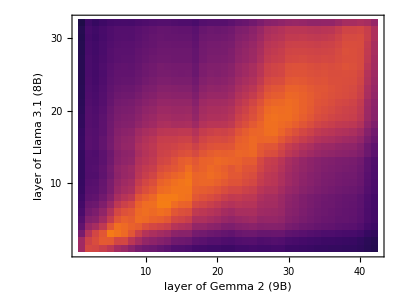

```mathematica
Export[FileNameJoin[{figureDirectory,"simple.pdf"}],
Echo@simplePlot[allMKNN["web_text"],"meta-llama/Meta-Llama-3.1-8B","google/gemma-2-9b"]
];
```

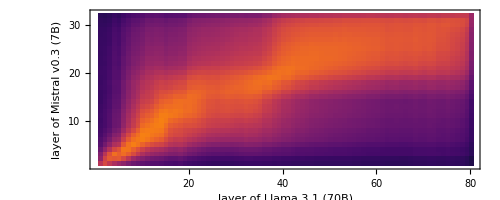

```mathematica
Export[FileNameJoin[{figureDirectory,"simple_2.pdf"}],
Echo@simplePlot[allMKNN["web_text"],"mistralai/Mistral-7B-v0.3","meta-llama/Llama-3.1-70B"]
];
```

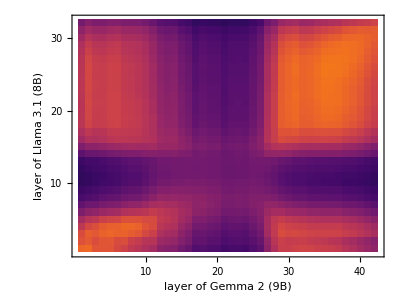

```mathematica
Export[FileNameJoin[{figureDirectory,"simple_random.pdf"}],
Echo@simplePlot[allMKNN["random_strings"],"meta-llama/Meta-Llama-3.1-8B","google/gemma-2-9b"]
];
```

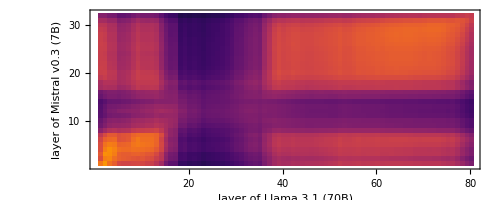

```mathematica
Export[FileNameJoin[{figureDirectory,"simple_random_2.pdf"}],
Echo@simplePlot[allMKNN["random_strings"],"mistralai/Mistral-7B-v0.3","meta-llama/Llama-3.1-70B"]
];
```

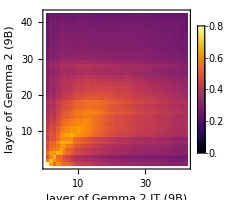

```mathematica
Export[FileNameJoin[{figureDirectory,"it_ifeval.pdf"}],
Echo@simplePlot[allMKNN["ifeval"],"google/gemma-2-9b","google/gemma-2-9b-it",ImageSize->200,PlotLegends->BarLegend[{Automatic,{0,maxPlotValue}}]]
];
```

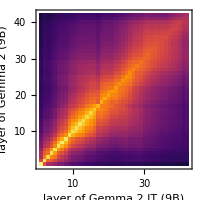

```mathematica
Export[FileNameJoin[{figureDirectory,"it_web_text.pdf"}],
Echo@simplePlot[allMKNN["web_text"],"google/gemma-2-9b","google/gemma-2-9b-it",ImageSize->200,PlotLegends->None]
];
```

### Example texts

```mathematica
texts=Normal@getKNNDataset[{"meta-llama/Meta-Llama-3.1-8B","web_text"}][[All,"text"]];
t=1001;
```

```mathematica
getNearestTexts[texts_,modelDataset_,layer_,text_,k_]:=texts[[Normal@getKNN[modelDataset,k][[layer,text]]+1]]
```

```mathematica
formatTableText[t0_,l_:70]:=
With[{t=StringReplace[t0,"\n\n"->" "]},
StringTake[t,UpTo[l]]<>If[StringLength[t]>l,"...",""]]
```

```mathematica
CopyToClipboard@formatTableText[texts[[t]],80]
```

```mathematica
texts[[t]]
```

```mathematica
tableCharacterLength=80;
```

```mathematica
nt1=getNearestTexts[texts,{"meta-llama/Meta-Llama-3.1-8B","web_text"},10,t,10];
nt2=getNearestTexts[texts,{"google/gemma-2-9b","web_text"},20,t,10];
nt3=getNearestTexts[texts,{"meta-llama/Meta-Llama-3.1-8B","web_text"},30,t,10];
nt4=getNearestTexts[texts,{"google/gemma-2-9b","web_text"},40,t,10];
```

#### Venn diagram version

```mathematica
texts=Join[
EchoFunction[Length]@Complement[nt1,nt2],
EchoFunction[Length]@Intersection[nt1,nt2],
EchoFunction[Length]@Complement[nt2,nt1]
];
```

3

7

3

```mathematica
CopyToClipboard@StringRiffle[
"\\small\\verb^"<>formatTableText[#,tableCharacterLength]<>"^"&/@texts,
" \\\\\n"
]
```

#### Text version

```mathematica
CopyToClipboard@StringRiffle[
"\\item["<>If[MemberQ[nt2,#],"\\matchMark","\\unmatchMark"]<>"]\\begin{verbatim}"<>formatTableText[#,tableCharacterLength]<>"\\end{verbatim}"&/@nt1,
"\n"
]
```

```mathematica
CopyToClipboard@StringRiffle[
"\\item["<>If[MemberQ[nt1,#],"\\matchMark","\\unmatchMark"]<>"]\\begin{verbatim}"<>formatTableText[#,tableCharacterLength]<>"\\end{verbatim}"&/@nt2,
"\n"
]
```

```mathematica
CopyToClipboard@StringRiffle[
"\\item["<>If[MemberQ[nt4,#],"\\matchMark","\\unmatchMark"]<>"]\\begin{verbatim}"<>formatTableText[#,tableCharacterLength]<>"\\end{verbatim}"&/@nt3,
"\n"
]
```

```mathematica
CopyToClipboard@StringRiffle[
"\\item["<>If[MemberQ[nt3,#],"\\matchMark","\\unmatchMark"]<>"]\\begin{verbatim}"<>formatTableText[#,tableCharacterLength]<>"\\end{verbatim}"&/@nt4,
"\n"
]
```

```mathematica
Length@Intersection[nt1,nt2]
```

7

```mathematica
Length@Intersection[nt1,nt3]
```

0

```mathematica
Length@Intersection[nt2,nt4]
```

2

```mathematica
Length@Intersection[nt2,nt3]
```

0

### Big plots (square)

```mathematica
bigPlotSquare[mknn_,models_,imgSize_:100,opts:OptionsPattern[Graphics]]:=
Module[{imgs,i,horizTicks,vertTicks},

imgs=Table[
Image[Map[infernoColors,Reverse@lookupMKNN[mknn,{m1,m2}],{2}]],
{m1,models},{m2,models}
];

i=ImageAssemble@Reverse@Map[ImageResize[#,{imgSize,imgSize},Resampling->"Nearest"]&,imgs,{2}];

horizTicks=MapIndexed[
{First[#2]*imgSize-imgSize/2,modelDisplayNames@#1,{0,0.01}}&,
models
];
vertTicks=MapIndexed[
{First[#2]*imgSize-imgSize/2,Rotate[modelDisplayNames@#1,Pi/2],{0,0.01}}&,
models
];

Graphics[
i,
opts,
PlotRangePadding->None,
Frame->{{True,False},{False,True}},
FrameTicks->{{horizTicks,horizTicks},{vertTicks,vertTicks}}
]
]
```

```mathematica
KeyValueMap[
Export[FileNameJoin[{figureDirectory,#1<>"_big_mat_square.pdf"}],
bigPlotSquare[#2/maxPlotValue,modelShortList,100,ImageSize->600]
]&,
allMKNN
];
```

```mathematica
KeyValueMap[
Export[FileNameJoin[{figureDirectory,#1<>"_mega_mat_square.pdf"}],
Legended[
bigPlotSquare[#2/maxPlotValue,allModels,100,ImageSize->900],
Placed[BarLegend[{infernoColors[#/maxPlotValue]&,{0,maxPlotValue}},LegendLayout->"Row"],Below]
]
]&,
allMKNN
];
```

### Big plots (rectangular)

```mathematica
Options[bigPlotRectangular]=Join[
Options[ArrayPlot],
{
"RotateTicks"->True
}
];
bigPlotRectangular[mknn_,models_,opts:OptionsPattern[]]:=
Module[{mat,modelLayers,modelPositions,rotateTicks,horizTicks,vertTicks},

mat=ArrayFlatten@Table[
lookupMKNN[mknn,{m1,m2}],
{m1,models},{m2,models}
];

modelLayers=AssociationMap[Length@lookupMKNN[mknn,{#,models[[1]]}]&,models];
modelPositions=Prepend[Accumulate[Lookup[modelLayers,models]],0];

rotateTicks=OptionValue["RotateTicks"];
horizTicks=MapThread[
{#1,Rotate[modelDisplayNames@#2,If[rotateTicks,0,Pi/2]],{0,0.01}}&,
{Mean[{Most@modelPositions,Rest@modelPositions}],models}
];
vertTicks=MapThread[
{#1,Rotate[modelDisplayNames@#2,If[rotateTicks,Pi/2,0]],{0,0.01}}&,
{Mean[{Most@modelPositions,Rest@modelPositions}],models}
];

ArrayPlot[
mat,
FilterRules[{opts},Options[ArrayPlot]],
DataReversed->True,
ColorFunction->infernoColors,
ColorFunctionScaling->False,
PlotRangePadding->None,
Frame->{{True,False},{False,True}},
FrameTicks->{{horizTicks,horizTicks},{vertTicks,vertTicks}}(*,
GridLines->{modelPositions,modelPositions},
GridLinesStyle->Directive[Green,Opacity[1]]*)
]
]
```

```mathematica
KeyValueMap[
Export[FileNameJoin[{figureDirectory,#1<>"_big_mat_rectangular.pdf"}],
bigPlotRectangular[#2/maxPlotValue,modelShortList,ImageSize->600]
]&,
allMKNN
];
```

```mathematica
KeyValueMap[
Export[FileNameJoin[{figureDirectory,#1<>"_mega_mat_rectangular.pdf"}],
Legended[
bigPlotRectangular[#2/maxPlotValue,allModels,ImageSize->900],
Placed[BarLegend[{infernoColors[#/maxPlotValue]&,{0,maxPlotValue}},LegendLayout->"Row"],Below]
]
]&,
allMKNN
];
```

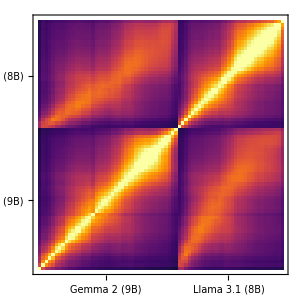

```mathematica
p=bigPlotRectangular[allMKNN["web_text"]/maxPlotValue,Reverse@{"meta-llama/Meta-Llama-3.1-8B","google/gemma-2-9b"},ImageSize->300,"RotateTicks"->False]
```

```mathematica
Export[FileNameJoin[{figureDirectory,"affinity_2x2.pdf"}],p];
```

### Translation plots

```mathematica
maxTranslationPlotValue=0.25;
```

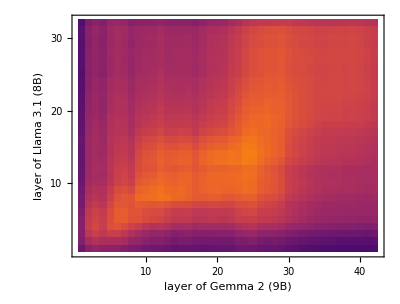

```mathematica
p=simplePlot[
allMKNNTranslations,"meta-llama/Meta-Llama-3.1-8B","google/gemma-2-9b",
"MaxPlotValue"->maxTranslationPlotValue
]
```

```mathematica
Export[FileNameJoin[{figureDirectory,"translations.pdf"}],p];
```

```mathematica
Export[FileNameJoin[{figureDirectory,"translations_big_mat_square.pdf"}],
bigPlotSquare[allMKNNTranslations/maxTranslationPlotValue,modelShortList,100,ImageSize->600]
];
```

```mathematica
Export[FileNameJoin[{figureDirectory,"translations_mega_mat_square.pdf"}],
Legended[
bigPlotSquare[allMKNNTranslations/maxTranslationPlotValue,allModels,100,ImageSize->900],
Placed[BarLegend[{infernoColors[#/maxTranslationPlotValue]&,{0,maxTranslationPlotValue}},LegendLayout->"Row"],Below]
]
];
```

```mathematica
Export[FileNameJoin[{figureDirectory,"translations_big_mat_rectangular.pdf"}],
bigPlotRectangular[allMKNNTranslations/maxTranslationPlotValue,modelShortList,ImageSize->600]
];
```

```mathematica
Export[FileNameJoin[{figureDirectory,"translations_mega_mat_rectangular.pdf"}],
Legended[
bigPlotRectangular[allMKNNTranslations/maxTranslationPlotValue,allModels,ImageSize->900],
Placed[BarLegend[{infernoColors[#/maxTranslationPlotValue]&,{0,maxTranslationPlotValue}},LegendLayout->"Row"],Below]
]
];
```

### Average similarity

```mathematica
averageSimilarityPlot[mknns_,models_,binSize_,scaleMax_,opts___]:=
Module[{mknnMats,pointValues,mat},
mknnMats=Catenate@Table[
lookupMKNN[mknns,{m1,m2}],
{m1,models},{m2,DeleteCases[models,m1]}
];

pointValues=Catenate@Map[
mat|->Catenate@MapIndexed[N@#2/Dimensions[mat]->#1&,mat,{2}],
mknnMats
];

mat=Map[Mean,BinLists[pointValues,binSize,binSize],{2}];

ArrayPlot[
Reverse@mat,
opts,
DataReversed->False,
DataRange->{{0,1},{0,1}},
ColorFunction->(infernoColors[#/scaleMax]&),
ColorFunctionScaling->False,
PlotLegends->BarLegend[{Automatic,{0,scaleMax}}],
PlotRangePadding->None,
Frame->{{True,False},{True,False}},
FrameTicks->All,
FrameLabel->{"depth in model 2","depth in model 1"}
]
]
```

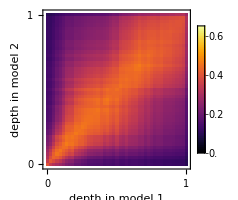

```mathematica
Export[FileNameJoin[{figureDirectory,"averageSimilarity.pdf"}],Echo@averageSimilarityPlot[allMKNN["web_text"],allModels,1/45,0.65,ImageSize->200]];
```

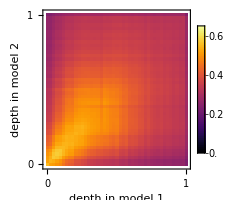

```mathematica
averageSimilarityPlot[allMKNN["ifeval"],allModels,1/45,0.65,ImageSize->200]
```

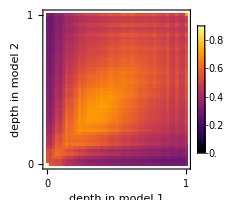

```mathematica
averageSimilarityPlot[allMKNN["ifeval"],chatModels,1/45,0.9,ImageSize->200]
```

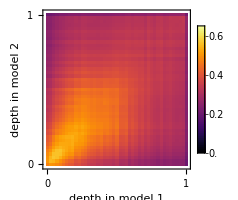

```mathematica
averageSimilarityPlot[allMKNN["ifeval"],Complement[allModels,chatModels],1/45,0.65,ImageSize->200]
```

### Max similarity

```mathematica
maxSimilarityPlot[mknns_,models_,opts___]:=
Module[{mknnMats},
mknnMats=Catenate@Table[
lookupMKNN[mknns,{m1,m2}],
{m1,models},{m2,DeleteCases[models,m1]}
];

ListLinePlot[
Map[Max,mknnMats,{2}],
opts,
PlotRange->{{0,1},{0,1}},
DataRange->{0,1},
PlotStyle->Directive[Opacity[0.2],Thickness[0.003],RGBColor[0.24,0.6,0.8](*ColorData[97][1]*)],
Frame->True,
FrameLabel->{"layer depth","max similarity to other model"},
AspectRatio->Automatic
]
]
```

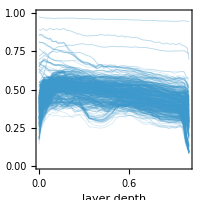

```mathematica
Export[FileNameJoin[{figureDirectory,"maxSimilarity.pdf"}],Echo@maxSimilarityPlot[allMKNN["web_text"],allModels,ImageSize->200]];
Export[FileNameJoin[{figureDirectory,"maxSimilarity.png"}],maxSimilarityPlot[allMKNN["web_text"],allModels,ImageSize->200],RasterSize->1500];
```

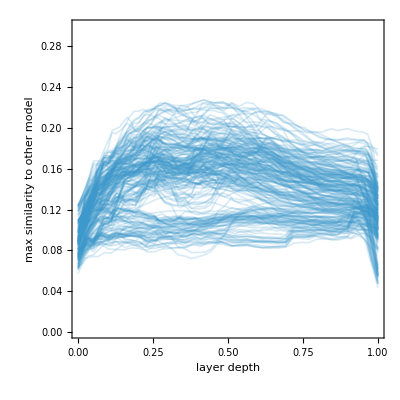

```mathematica
maxSimilarityPlot[allMKNNTranslations,Complement[allModels,chatModels],PlotRange->{{0,1},{0,0.3}},AspectRatio->1]
```

### Max similarity depth

```mathematica
maxSimilarityDepthPlot[mknns_,models_,opts___]:=
Module[{mknnMats,mknnPaths},
mknnMats=Catenate@Table[
lookupMKNN[mknns,{m1,m2}],
{m1,models},{m2,DeleteCases[models,m1]}
];

mknnPaths=Map[
mat|->MapIndexed[N@{First[#2],Ordering[#1,-1][[1]]}/Dimensions[mat]&,mat],
mknnMats
];

ListLinePlot[
mknnPaths,
opts,
PlotStyle->Directive[Opacity[0.2],Thickness[0.003],RGBColor[0.24,0.6,0.8](*ColorData[97][1]*)],
AspectRatio->Automatic,
PlotRange->{{0,1},{0,1}},
Frame->True,
FrameLabel->{"depth in model 1","most similar depth in model 2"}
]
]
```

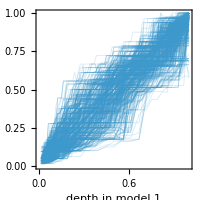

```mathematica
Export[FileNameJoin[{figureDirectory,"maxSimilarityDepth.pdf"}],Echo@maxSimilarityDepthPlot[allMKNN["web_text"],allModels,ImageSize->200]];
Export[FileNameJoin[{figureDirectory,"maxSimilarityDepth.png"}],maxSimilarityDepthPlot[allMKNN["web_text"],allModels,ImageSize->200],RasterSize->1500];
```

### Null model

```mathematica
mknnDist=HypergeometricDistribution[k,k,n-1]
```

HypergeometricDistribution[k,k,-1+n]

```mathematica
(*sampleMeanMKNNDist=NormalDistribution[Mean[mknnDist],Sqrt[Variance[mknnDist]/n]]*)
sampleMeanMKNNDist=NormalDistribution[Mean[mknnDist]/k,Sqrt[Variance[mknnDist]/n]/k]
```

NormalDistribution[k/(-1+n),(√((k^2 (1-k/(-1+n)) (-1-k+n))/((-2+n) (-1+n) n)))/k]

```mathematica
FullSimplify@sampleMeanMKNNDist
```

NormalDistribution[k/(-1+n),(√((k^2 (1+k-n)^2)/((-2+n) (-1+n)^2 n)))/k]

```mathematica
PDF[sampleMeanMKNNDist/.{k->10,n->2048},0.4]
```

2.283366096×10^-143444

```mathematica
CDF[sampleMeanMKNNDist/.{k->10,n->2048},Rationalize[0.4]]
```

1/2 Erfc[-(43136 √2046)/3395]

```mathematica
Log10[1-1/2Erfc[N[-(43136 √2046)/3395,25]]]
```

-143449.86463761801010945

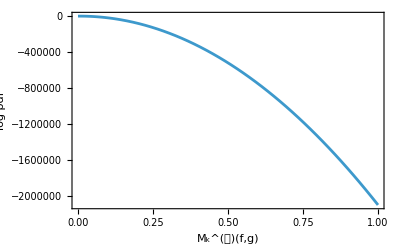

```mathematica
p=Plot[
Evaluate@Log@PDF[sampleMeanMKNNDist/.{k->10,n->2048},x],{x,0,1},
PlotRange->{{0,1},All},
WorkingPrecision->100,
Frame->True,
FrameLabel->{"M_k^(𝒟)(f,g)","log pdf"},
ImageSize->400
]
```

```mathematica
Export[FileNameJoin[{figureDirectory,"nullDistribution.pdf"}],p];
```

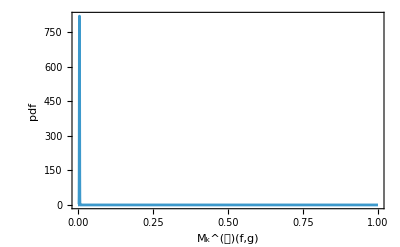

```mathematica
Plot[
Evaluate@PDF[sampleMeanMKNNDist/.{k->10,n->2048},x],{x,0,1},
PlotRange->{{0,1},All},
WorkingPrecision->100,
Frame->True,
FrameLabel->{"M_k^(𝒟)(f,g)","pdf"},
ImageSize->400
]
```

### Model table

```mathematica
modelLayers=AssociationMap[Length@lookupMKNN[allMKNN["web_text"],{#,allModels[[1]]}]&,allModels];
```

```mathematica
CopyToClipboard@StringJoin[
StringRiffle[{
modelDisplayNames[#],
modelLayers[#],
If[MemberQ[chatModels,#],"Yes","No"],
StringTemplate["\\href{https://huggingface.co/`1`}{`1`}"][#]
}," & "]<>" \\\\\n"&/@allModels
]
```

### Other values of k

```mathematica
bigKNN1=getKNN[{"meta-llama/Meta-Llama-3.1-8B","web_text"},100];
bigKNN2=getKNN[{"google/gemma-2-9b","web_text"},100];
```

```mathematica
Do[
Module[{p},
p=mknnPlot[
Outer[computeMKNN,bigKNN1[[All,All,;;k]],bigKNN2[[All,All,;;k]],1],
maxPlotValue,
FrameLabel->{"layer of "<>modelDisplayNames["meta-llama/Meta-Llama-3.1-8B"],"layer of "<>modelDisplayNames["google/gemma-2-9b"]},
PlotLabel->With[{v=k},ToString[Unevaluated[k==v],TraditionalForm]],
PlotLegends->BarLegend[{Automatic,{0,maxPlotValue}}],
ImageSize->300
];

Export[FileNameJoin[{figureDirectory,StringTemplate["simple_k_``.pdf"][k]}],Echo@p]
],
{k,{1,10,50,100}}
]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

### Generalized diagonal tests

```mathematica
generalizedDiagonalMatrix[{n_,m_}]/;n>m:=Table[Boole[j<=i<=j+n-m],{i,n},{j,m}]
generalizedDiagonalMatrix[{n_,m_}]/;n<m:=Transpose@generalizedDiagonalMatrix[{m,n}]
generalizedDiagonalMatrix[{n_,m_}]/;n==m:=IdentityMatrix[n]
```

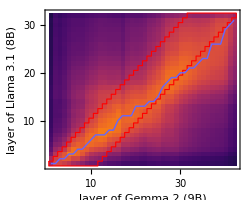

```mathematica
p=Module[{mknn,mesh,maxPositions},
mknn=lookupMKNN[allMKNN["web_text"],{"meta-llama/Meta-Llama-3.1-8B","google/gemma-2-9b"}];

mesh=ImageMesh[Image@Reverse@generalizedDiagonalMatrix@Dimensions@mknn,Method->"Exact"];

maxPositions=Ordering[#,-1][[1]]&/@Transpose[mknn];

First@simplePlot[allMKNN["web_text"],"meta-llama/Meta-Llama-3.1-8B","google/gemma-2-9b",
Epilog->{
EdgeForm[{Red,Thick}],FaceForm[(*{Red,Opacity[0.3]}*)],mesh,
Thick(*,Darker[Cyan,0.2]*),Lighter[Blue,0.4],Line@MapIndexed[{First[#2]-0.5,#1-0.5}&,maxPositions]
},
ImageSize->250
]
]
```

```mathematica
Export[FileNameJoin[{figureDirectory,"diagonal_and_monotonicity.pdf"}],p];
```

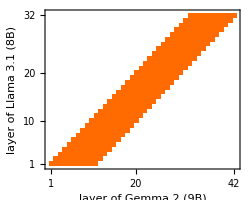

```mathematica
p=MatrixPlot[
generalizedDiagonalMatrix@Dimensions@lookupMKNN[allMKNN["web_text"],{"meta-llama/Meta-Llama-3.1-8B","google/gemma-2-9b"}],
DataReversed->True,
Frame->True,
FrameLabel->{"layer of "<>modelDisplayNames["meta-llama/Meta-Llama-3.1-8B"],"layer of "<>modelDisplayNames["google/gemma-2-9b"]},
ImageSize->250
]
```

```mathematica
Export[FileNameJoin[{figureDirectory,"generalized_diagonal.pdf"}],p];
```

```mathematica
mknnMats=Catenate@Table[
lookupMKNN[allMKNN["web_text"],{m1,m2}],
{m1,allModels},{m2,DeleteCases[allModels,m1]}
];
```

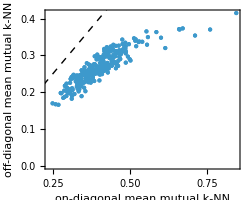

```mathematica
p=ListPlot[
{
Mean@Catenate@Pick[#,generalizedDiagonalMatrix@Dimensions@#,1],Mean@Catenate@Pick[#,generalizedDiagonalMatrix@Dimensions@#,0]
}&/@mknnMats,
Epilog->{Dashed,InfiniteLine[{0,0},{1,1}]},
AspectRatio->Automatic,
PlotRange->All,
Frame->True,
PlotStyle->PointSize[Small],
FrameLabel->{"on-diagonal mean mutual k-NN","off-diagonal mean mutual k-NN"},
ImageSize->250
]
```

```mathematica
Export[FileNameJoin[{figureDirectory,"on_off_diagonal_means.pdf"}],p];
```

```mathematica
pvalues=TTest[{
Catenate@Pick[#,generalizedDiagonalMatrix@Dimensions@#,1],
Catenate@Pick[#,generalizedDiagonalMatrix@Dimensions@#,0]
},
AlternativeHypothesis->"Greater",
VerifyTestAssumptions->None
]&/@mknnMats;
```

General::munfl: 3.06647688313060394363632×10^-339 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.99952455418391103325231×10^-317 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 8.54679178912259555613399×10^-328 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
MinMax[pvalues]
```

{0.,8.02725×10^-7}

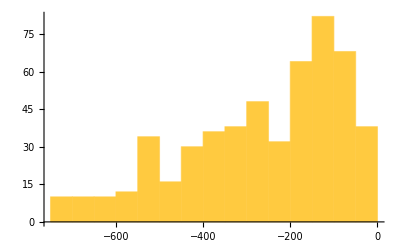

```mathematica
Histogram[Log@pvalues,20]
```

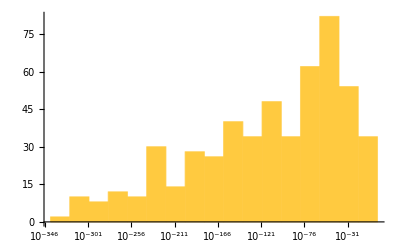

```mathematica
Histogram[pvalues,{"Log",Automatic}]
```

### Monotonicity tests

```mathematica
monotonicProb[dists_]:=Total[Fold[Accumulate[#1*#2]&,1,Most@dists]*Last[dists]]
```

```mathematica
monotonicityRatio[mknn_]:=
Module[{dists,nullDists},
dists=Normalize[#,Total]&/@mknn;
nullDists=ConstantArray[N@1/Dimensions[dists][[2]],Dimensions[dists]];
monotonicProb[dists]/monotonicProb[nullDists]
]
```

```mathematica
monotonicityRatio2[mknn_]:=
Module[{dists,nullDists},
dists=Normalize[#,Total]&/@mknn;
nullDists=RandomSample[dists];
monotonicProb[dists]/monotonicProb[nullDists]
]
```

```mathematica
getMKNNMatsNoIdent[allMKNN_,models_]:=
Catenate@Table[
lookupMKNN[allMKNN,{m1,m2}],
{m1,models},{m2,DeleteCases[models,m1]}
]
```

```mathematica
mknnMats=Catenate@Table[
lookupMKNN[allMKNN["web_text"],{m1,m2}],
{m1,allModels},{m2,DeleteCases[allModels,m1]}
];
```

```mathematica
MinMax[monotonicityRatio/@getMKNNMatsNoIdent[allMKNN["web_text"],allModels]]
```

{45.4589,5.14983×10^20}

```mathematica
MinMax[monotonicityRatio2/@getMKNNMatsNoIdent[allMKNN["web_text"],allModels]]
```

{16.3458,2.50136×10^23}

```mathematica
MinMax[monotonicityRatio/@getMKNNMatsNoIdent[allMKNN["random_strings"],allModels]]
```

{2.79834,5.20621×10^14}

```mathematica
MinMax[monotonicityRatio2/@getMKNNMatsNoIdent[allMKNN["random_strings"],allModels]]
```

{1.90131,6.89826×10^15}

```mathematica
Ordering[monotonicityRatio/@getMKNNMatsNoIdent[allMKNN["random_strings"],allModels],-1]
```

{289}

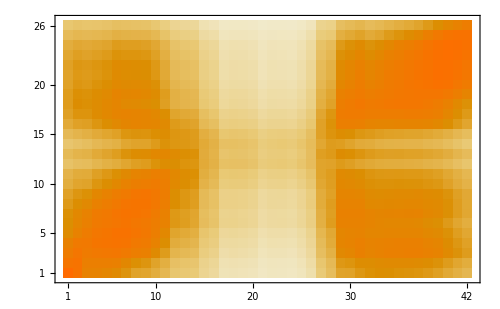

```mathematica
MatrixPlot[allMKNN["random_strings"][[50]],DataReversed->True]
```

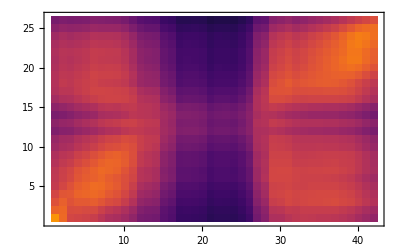

```mathematica
mknnPlot@allMKNN["random_strings"][[50]]
```

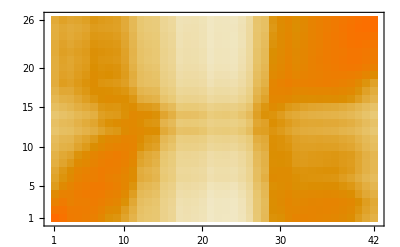

```mathematica
MatrixPlot[Normalize[#,Total]&/@allMKNN["random_strings"][[50]],DataReversed->True]
```

```mathematica
MatrixPlot[Normalize[#,Total]&/@allMKNN["random_strings"][[289]]]
```

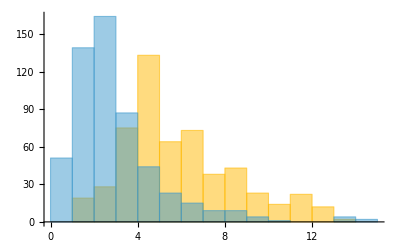

```mathematica
Histogram[{
Log10[monotonicityRatio/@getMKNNMatsNoIdent[allMKNN["web_text"],allModels]],
Log10[monotonicityRatio/@getMKNNMatsNoIdent[allMKNN["random_strings"],allModels]]
}]
```

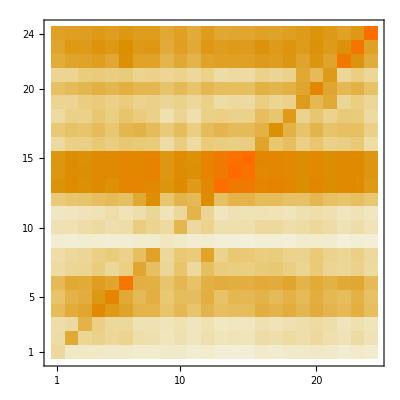

```mathematica
MatrixPlot[
Log10@Table[
monotonicityRatio@lookupMKNN[allMKNN["web_text"],{m1,m2}],
{m1,allModels},{m2,allModels}
],
DataReversed->True
]
```

#### Validation example

Run a simulation and test whether it matches the monitonicProb function:

```mathematica
mknn=lookupMKNN[allMKNN["web_text"],{"google/gemma-2-9b","meta-llama/Meta-Llama-3.1-8B"}];
```

```mathematica
dists=Normalize[#,Total]&/@mknn;
```

```mathematica
Mean[Boole[LessEqual@@#]&/@Transpose[{
RandomChoice[dists[[1]]->Range[Length[dists[[1]]]],1000000],
RandomChoice[dists[[2]]->Range[Length[dists[[1]]]],1000000],
RandomChoice[dists[[3]]->Range[Length[dists[[1]]]],1000000]
}]]//N
```

0.183021

```mathematica
monotonicProb[dists[[;;3]]]
```

0.183802

### Rank correlation

Do the rank correlation of the means of each column

```mathematica
mknnMats=Catenate@Table[
lookupMKNN[allMKNN["web_text"],{m1,m2}],
{m1,allModels},{m2,DeleteCases[allModels,m1]}
];
```

#### Maxes

```mathematica
pvalues=(mknn|->SpearmanRankTest[Range@Length@mknn,Ordering[#,-1][[1]]&/@mknn])/@mknnMats;
```

```mathematica
MinMax[pvalues]
```

{0.,8.74864×10^-11}

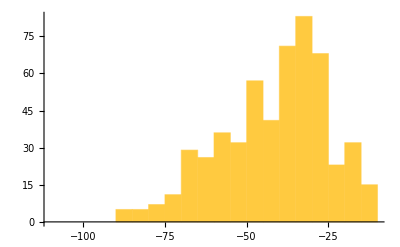

```mathematica
Histogram[Log10@pvalues]
```

```mathematica
correlations=(mknn|->SpearmanRho[Range@Length@mknn,Ordering[#,-1][[1]]&/@mknn])/@mknnMats;
```

```mathematica
N@MinMax[correlations]
```

{0.953963,1.}

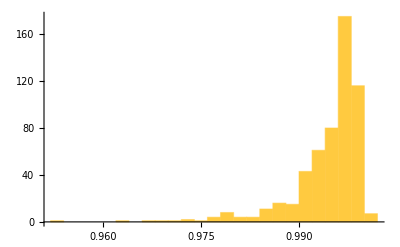

```mathematica
Histogram[correlations]
```

#### Means

```mathematica
vectorMean[v_]:=Range[Length[v]].Normalize[v,Total]
```

```mathematica
pvalues=(mknn|->SpearmanRankTest[Range@Length@mknn,vectorMean/@mknn])/@mknnMats;
```

```mathematica
MinMax[pvalues]
```

{0.,1.55232×10^-12}

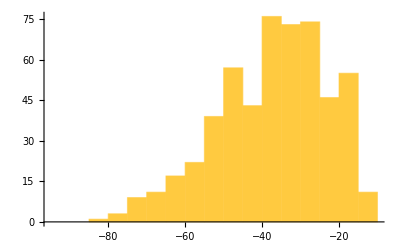

```mathematica
Histogram[Log10@pvalues]
```

```mathematica
correlations=(mknn|->SpearmanRho[Range@Length@mknn,vectorMean/@mknn])/@mknnMats;
```

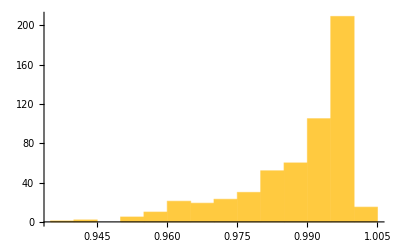

```mathematica
Histogram[correlations]
```

## Scratch space

### Simple plots

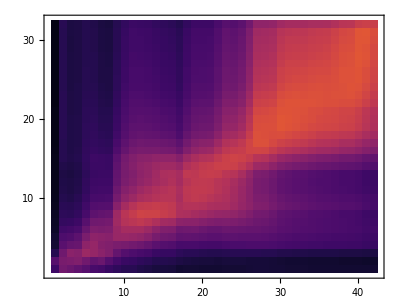

```mathematica
mknnPlot@Outer[computeMKNN,
Normal@getKNN[{"meta-llama/Meta-Llama-3.1-8B","wikipedia"}],
Normal@getKNN[{"google/gemma-2-9b","wikipedia"}],
1]
```

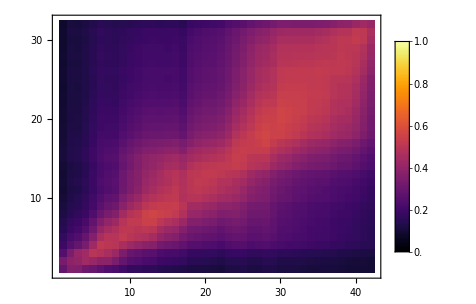

```mathematica
mknnPlot@Outer[computeMKNN,
Normal@getKNN[{"meta-llama/Meta-Llama-3.1-8B","imdb"}],
Normal@getKNN[{"google/gemma-2-9b","imdb"}],
1]
```

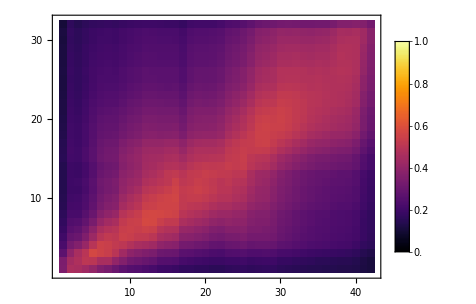

```mathematica
mknnPlot@Outer[computeMKNN,
Normal@getKNN[{"meta-llama/Meta-Llama-3.1-8B","web_text"}],
Normal@getKNN[{"google/gemma-2-9b","web_text"}],
1]
```

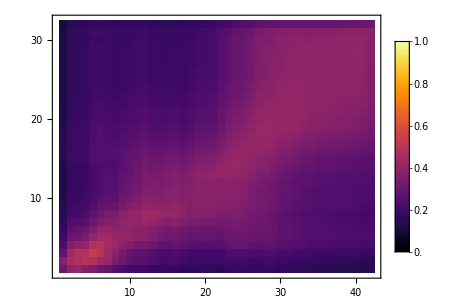

```mathematica
mknnPlot@Outer[computeMKNN,
Normal@getKNN[{"meta-llama/Meta-Llama-3.1-8B","book_translations_en"}],
Normal@getKNN[{"google/gemma-2-9b","book_translations_en"}],
1]
```

### Example texts

```mathematica
texts=Normal@getKNNDataset[{"meta-llama/Meta-Llama-3.1-8B","web_text"}][[All,"text"]];
t=1001;
```

```mathematica
getNearestTexts[texts_,modelDataset_,layer_,text_,k_]:=texts[[Normal@getKNN[modelDataset,k][[layer,text]]+1]]
```

```mathematica
formatTableText[t0_,l_:70]:=
With[{t=StringReplace[t0,"\n\n"->" "]},
StringTake[t,UpTo[l]]<>If[StringLength[t]>l,"...",""]]
```

```mathematica
CopyToClipboard@formatTableText[texts[[t]],80]
```

```mathematica
texts[[t]]
```

```mathematica
nt1=getNearestTexts[texts,{"meta-llama/Meta-Llama-3.1-8B","web_text"},10,t,10];
nt2=getNearestTexts[texts,{"google/gemma-2-9b","web_text"},20,t,10];
```

```mathematica
CopyToClipboard@StringRiffle[
"\\item["<>If[MemberQ[nt2,#],"\\matchMark","\\unmatchMark"]<>"]\\begin{verbatim}"<>formatTableText[#,70]<>"\\end{verbatim}"&/@nt1,
"\n"
]
```

```mathematica
CopyToClipboard@StringRiffle[
"\\item["<>If[MemberQ[nt1,#],"\\matchMark","\\unmatchMark"]<>"]\\begin{verbatim}"<>formatTableText[#,70]<>"\\end{verbatim}"&/@nt2,
"\n"
]
```

```mathematica
nt3=getNearestTexts[texts,{"meta-llama/Meta-Llama-3.1-8B","web_text"},30,t,10];
nt4=getNearestTexts[texts,{"google/gemma-2-9b","web_text"},40,t,10];
```

```mathematica
CopyToClipboard@StringRiffle[
"\\item["<>If[MemberQ[nt4,#],"\\matchMark","\\unmatchMark"]<>"]\\begin{verbatim}"<>formatTableText[#,70]<>"\\end{verbatim}"&/@nt3,
"\n"
]
```

```mathematica
CopyToClipboard@StringRiffle[
"\\item["<>If[MemberQ[nt3,#],"\\matchMark","\\unmatchMark"]<>"]\\begin{verbatim}"<>formatTableText[#,70]<>"\\end{verbatim}"&/@nt4,
"\n"
]
```

```mathematica
Length@Intersection[nt1,nt2]
```

7

```mathematica
Length@Intersection[nt1,nt3]
```

0

```mathematica
Length@Intersection[nt2,nt4]
```

2

```mathematica
Length@Intersection[nt2,nt3]
```

0

#### Old

```mathematica
nearestTexts=texts[[Normal@getKNN[{"meta-llama/Meta-Llama-3.1-8B","web_text"},5][[10,t]]+1]];
```

```mathematica
nearestTexts
```

```mathematica
texts=Normal@getKNNDataset[{"meta-llama/Meta-Llama-3.1-8B","wikipedia"}][[All,"text"]];
t=7;
nearestTexts1=texts[[Normal@getKNN[{"meta-llama/Meta-Llama-3.1-8B","wikipedia"},5][[10,t]]+1]];
nearestTexts2=texts[[Normal@getKNN[{"google/gemma-2-9b","wikipedia"},5][[17,t]]+1]];
```

```mathematica
Length@Intersection[nearestTexts,nearestTexts2]
```

0

```mathematica
mknnPlot@lookupMKNN[allMKNN,{"meta-llama/Meta-Llama-3.1-8B","google/gemma-2-9b"}]
```

```mathematica
formatTableText[t0_,l_:80]:=
With[{t=StringReplace[t0,"\n\n"->" "]},
StringTake[t,UpTo[l]]<>If[StringLength[t]>l,"...",""]]
```

```mathematica
CopyToClipboard[StringRiffle[
MapIndexed[
ToString@First@#2<>"&\\small\\texttt{"<>#1<>"}"&,
formatTableText/@nearestTexts
],
"\\\\\n"
]<>"\\\\\n"]
```

### Generalized diagonal

```mathematica
generalizedDiagonalMatrix[n_,m_]/;n>m:=Table[Boole[j<=i<=j+n-m],{i,n},{j,m}]
generalizedDiagonalMatrix[n_,m_]/;n<m:=Transpose@generalizedDiagonalMatrix[m,n]
generalizedDiagonalMatrix[n_,m_]/;n==m:=IdentityMatrix[n]
```

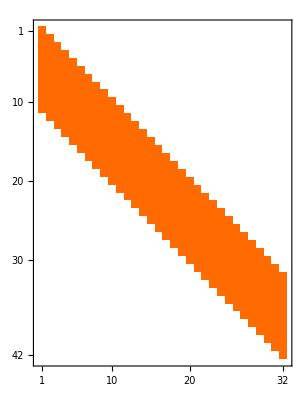

```mathematica
MatrixPlot[generalizedDiagonalMatrix@@Dimensions[mknn]]
```

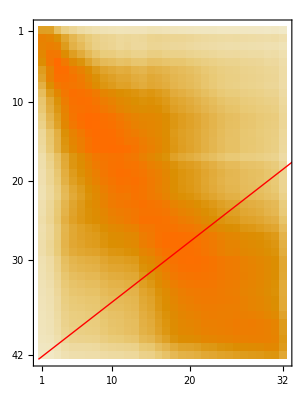

```mathematica
MatrixPlot[mknn,Epilog->{Red,Line[{{0,0},Dimensions[mknn]}]}]
```

```mathematica
onOffDiagonalMean[mknn_]:=With[{mask=generalizedDiagonalMatrix@@Dimensions[mknn]},
{Total[mknn*mask,2]/Total[mask,2],Total[mknn*(1-mask),2]/Total[(1-mask),2]}
]
```

```mathematica
onOffDiagonalMean@mknn
```

{0.465313,0.296484}

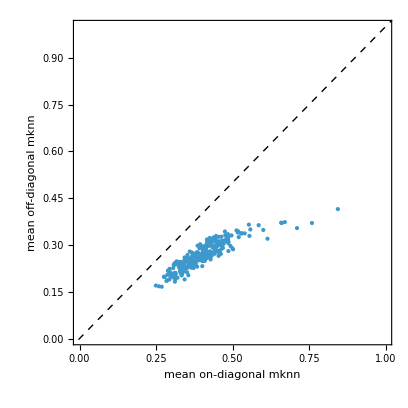

```mathematica
ListPlot[
onOffDiagonalMean[lookupMKNN[allMKNN,#]]&/@Discard[DeleteDuplicatesBy[Catenate@Outer[List,Keys@allKNN,Keys@allKNN],Sort],Apply@SameQ],
AspectRatio->Automatic,
Epilog->{Dashed,InfiniteLine[{0,0},{1,1}]},
PlotRange->{{0,1},{0,1}},
Frame->{{True,False},{True,False}},
FrameLabel->{"mean on-diagonal mknn","mean off-diagonal mknn"}
]
```

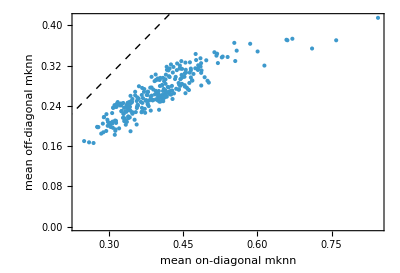

```mathematica
ListPlot[
onOffDiagonalMean[lookupMKNN[allMKNN,#]]&/@Discard[DeleteDuplicatesBy[Catenate@Outer[List,Keys@allKNN,Keys@allKNN],Sort],Apply@SameQ],
AspectRatio->Automatic,
Epilog->{Dashed,InfiniteLine[{0,0},{1,1}]},
(*PlotRange->{{0,1},{0,1}},*)
PlotRange->All,
Frame->{{True,False},{True,False}},
FrameLabel->{"mean on-diagonal mknn","mean off-diagonal mknn"}
]
```

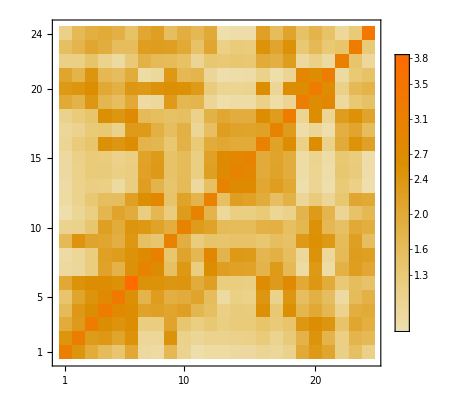

```mathematica
MatrixPlot[
Table[Divide@@onOffDiagonalMean@lookupMKNN[allMKNN,{m1,m2}],{m1,Keys@allKNN},{m2,Keys@allKNN}],
DataReversed->True,
PlotLegends->True
]
```

```mathematica
onOffDiagonalValues[mknn_]:=With[{mask=generalizedDiagonalMatrix@@Dimensions[mknn]},
{Catenate@MapThread[Pick[#1,#2,1]&,{mknn,mask}],Catenate@MapThread[Pick[#1,#2,1]&,{mknn,1-mask}]}
]
```

```mathematica
onOffDiagonalMean[lookupMKNN[allMKNN,#]]&/@Discard[DeleteDuplicatesBy[Catenate@Outer[List,Keys@allKNN,Keys@allKNN],Sort],Apply@SameQ]==(Mean/@onOffDiagonalValues[lookupMKNN[allMKNN,#]]&/@Discard[DeleteDuplicatesBy[Catenate@Outer[List,Keys@allKNN,Keys@allKNN],Sort],Apply@SameQ])
```

True

```mathematica
onOffVals=onOffDiagonalValues[lookupMKNN[allMKNN,#]]&/@Discard[DeleteDuplicatesBy[Catenate@Outer[List,Keys@allKNN,Keys@allKNN],Sort],Apply@SameQ];
```

```mathematica
pvalues=TTest[#,VerifyTestAssumptions->None]&/@onOffVals;
```

General::munfl: 3.06647688313060394363632×10^-339 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.99952455418391103325231×10^-317 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 8.54679178912259555613399×10^-328 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
pvaluesOneTailed=TTest[#,AlternativeHypothesis->"Greater",VerifyTestAssumptions->None]&/@onOffVals;
```

General::munfl: 3.06647688313060394363632×10^-339 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.99952455418391103325231×10^-317 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 8.54679178912259555613399×10^-328 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
MinMax[Subtract@@@Map[Mean,onOffVals,{2}]]
```

{0.069517,0.429078}

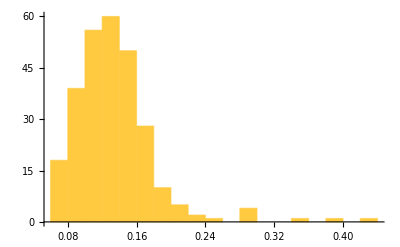

```mathematica
Histogram[Subtract@@@Map[Mean,onOffVals,{2}],PlotRange->All]
```

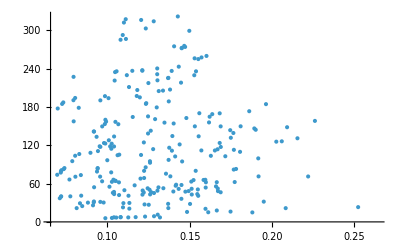

```mathematica
ListPlot[Transpose[{
Subtract@@@Map[Mean,onOffVals,{2}],
-Log10[pvalues]
}]]
```

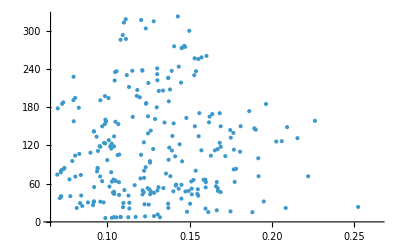

```mathematica
ListPlot[Transpose[{
Subtract@@@Map[Mean,onOffVals,{2}],
-Log10[pvaluesOneTailed]
}]]
```

### Monotonic random walks

```mathematica
mknn=lookupMKNN[allMKNN,{"google/gemma-2-9b","meta-llama/Meta-Llama-3.1-8B"}];
mknn=If[Dimensions[mknn][[1]]<Dimensions[mknn][[2]],Transpose[mknn],mknn];
```

```mathematica
dists=Normalize[#,Total]&/@mknn;
```

```mathematica
monotonicProb[dists_]:=Total[Fold[Accumulate[#1*#2]&,1,Most@dists]*Last[dists]]
```

```mathematica
Sum[dists[[1,i]]*dists[[2,j]]*dists[[3,k]],{i,1,Length[dists[[1]]]},{j,1,i},{k,1,j}]
```

0.184709

```mathematica
Count[Transpose[{
RandomChoice[dists[[1]]->Range[Length[dists[[1]]]],1000000],
RandomChoice[dists[[2]]->Range[Length[dists[[1]]]],1000000],
RandomChoice[dists[[3]]->Range[Length[dists[[1]]]],1000000]
}],{a_,b_,c_}/;a<=b<=c]/1000000//N
```

0.183466

```mathematica
monotonicProb@dists[[;;3]]
```

0.183802

```mathematica
Count[
Transpose@Table[RandomChoice[dists[[i]]->Range[Length[dists[[i]]]],1000000],{i,7}],
l_List/;LessEqual@@l
]/1000000//N
```

0.000458

```mathematica
monotonicProb@dists[[;;7]]
```

0.000398761

```mathematica
monotonicProb@dists
```

7.31329×10^-37

```mathematica
sumNestedTriangularSum2@Log@dists[[;;3]]
```

-63115.3

```mathematica
monotonicProb@ConstantArray[N@1/Dimensions[dists][[2]],Dimensions[dists]]
```

2.35136×10^-43

```mathematica
monotonicProb@dists
```

7.31329×10^-37

```mathematica
monotonicness[mknn_]:=
Module[{dists,nullDists},
dists=Normalize[#,Total]&/@mknn;
nullDists=ConstantArray[N@1/Dimensions[dists][[2]],Dimensions[dists]];
monotonicProb[dists]/monotonicProb[nullDists]
]
```

```mathematica
Log@monotonicness[mknn]
```

14.9502

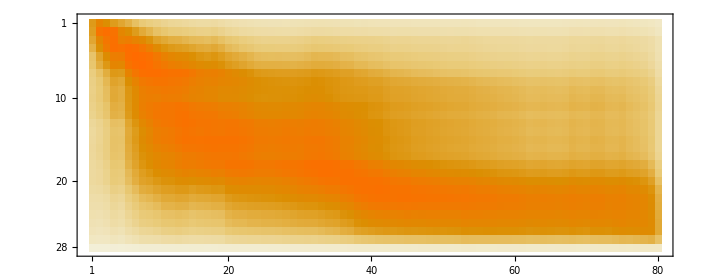

```mathematica
MatrixPlot@lookupMKNN[allMKNN,{"google/gemma-7b","meta-llama/Llama-3.1-70B"}]
```

```mathematica
monotonicness@lookupMKNN[allMKNN,{"meta-llama/Llama-3.1-70B","google/gemma-7b"}]
```

7.26578×10^10

```mathematica
bFactors=Table[monotonicness@lookupMKNN[allMKNN,{m1,m2}],{m1,Keys@allKNN},{m2,Keys@allKNN}];
```

```mathematica
MinMax@bFactors
```

{45.4589,8.04841×10^22}

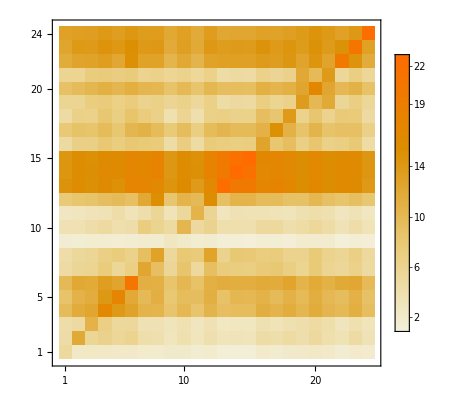

```mathematica
MatrixPlot[
Table[Log10@monotonicness@lookupMKNN[allMKNN,{m1,m2}],{m1,Keys@allKNN},{m2,Keys@allKNN}],
DataReversed->True,
PlotLegends->Automatic
]
```

### Max similarity plots

```mathematica
mknnMats=Catenate@Table[
lookupMKNN[allMKNN,{m1,m2}],
{m1,Keys@allKNN},{m2,DeleteCases[Keys@allKNN,m1]}
];
```

```mathematica
mknnPaths=Map[
mat|->MapIndexed[N@{First[#2],Ordering[#1,-1][[1]]}/Dimensions[mat]&,mat],
mknnMats
];
```

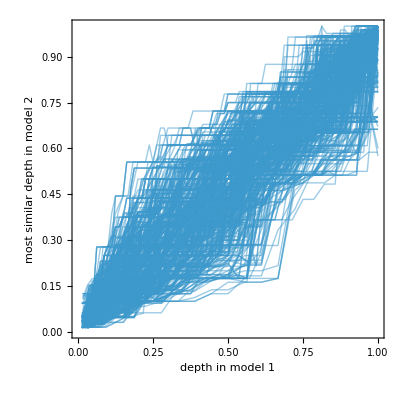

```mathematica
ListLinePlot[
mknnPaths,
PlotStyle->Directive[Opacity[0.5],Thin,RGBColor[0.24,0.6,0.8](*ColorData[97][1]*)],
AspectRatio->1,
PlotRange->{{0,1},{0,1}},
Frame->True,
FrameLabel->{"depth in model 1","most similar depth in model 2"}
]
```

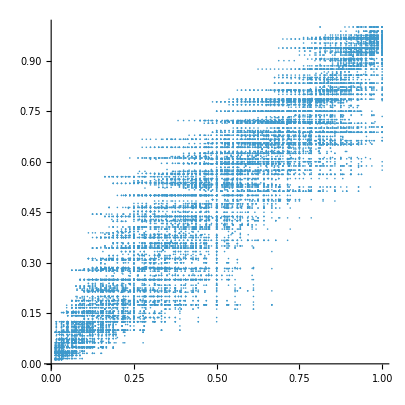

```mathematica
ListPlot[
Catenate@mknnPaths,
AspectRatio->1,
PlotRange->{{0,1},{0,1}}
]
```

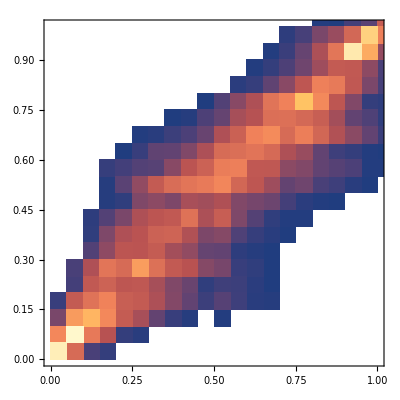

```mathematica
DensityHistogram[Catenate@mknnPaths,PlotRange->{{0,1},{0,1}}]
```

### Max column plots

```mathematica
mknnMats=Catenate@Table[
lookupMKNN[allMKNN["web_text"],{m1,m2}],
{m1,allModels},{m2,DeleteCases[allModels,m1]}
];
```

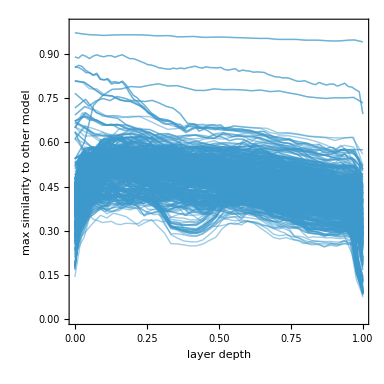

```mathematica
ListLinePlot[
Map[Max,mknnMats,{2}],PlotRange->{All,{0,1}},
DataRange->{0,1},
PlotStyle->Directive[Opacity[0.5],Thin,RGBColor[0.24,0.6,0.8](*ColorData[97][1]*)],
Frame->True,
FrameLabel->{"layer depth","max similarity to other model"},
AspectRatio->Automatic
]
```

### Aggregate plots

```mathematica
mknnMats=Catenate@Table[
lookupMKNN[allMKNN,{m1,m2}],
{m1,Keys@allKNN},{m2,DeleteCases[Keys@allKNN,m1]}
];
```

```mathematica
pointValues=Catenate@Map[
mat|->Catenate@MapIndexed[N@#2/Dimensions[mat]->#1&,mat,{2}],
mknnMats
];
```

```mathematica
mat=Map[Mean,BinLists[pointValues,1/45,1/45],{2}];
```

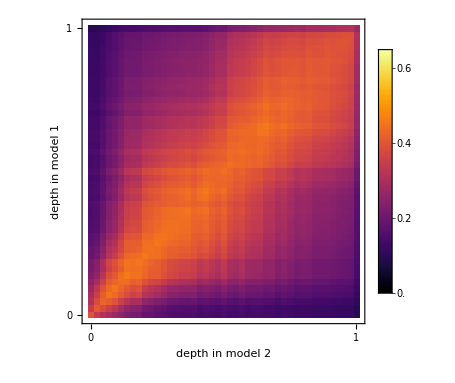

```mathematica
ArrayPlot[
Reverse@mat,
DataReversed->False,
DataRange->{{0,1},{0,1}},
ColorFunction->(infernoColors[#/0.65]&),
ColorFunctionScaling->False,
PlotLegends->BarLegend[{Automatic,{0,0.65}}],
PlotRangePadding->None,
Frame->{{True,False},{True,False}},
FrameTicks->All,
FrameLabel->{"depth in model 1","depth in model 2"}
]
```

### Square big mats

```mathematica
imgs=Table[
Image[Map[infernoColors,Reverse@lookupMKNN[allMKNN,{m1,m2}],{2}]],
{m1,Keys@allKNN},{m2,Keys@allKNN}
];
```

```mathematica
imgSize=100;
```

```mathematica
i=ImageAssemble@Reverse@Map[ImageResize[#,{imgSize,imgSize},Resampling->"Nearest"]&,imgs,{2}];
```

```mathematica
horizTicks=MapIndexed[
{First[#2]*imgSize-imgSize/2,modelDisplayNames@#1,{0,0.01}}&,
Keys@allKNN
];
vertTicks=MapIndexed[
{First[#2]*imgSize-imgSize/2,Rotate[modelDisplayNames@#1,Pi/2],{0,0.01}}&,
Keys@allKNN
];
```

```mathematica
Legended[
Graphics[
i,
PlotRangePadding->None,
Frame->{{True,False},{False,True}},
FrameTicks->{{horizTicks,horizTicks},{vertTicks,vertTicks}}
],
BarLegend[{infernoColors,{0,1}}]
]
```

-Graphics-

### Big mats

```mathematica
mat=ArrayFlatten@Table[
lookupMKNN[allMKNN,{m1,m2}],
{m1,allModels},{m2,allModels}
];
```

```mathematica
modelLayers=Length/@allKNN;
modelPositions=Prepend[Accumulate[Lookup[modelLayers,Keys@allKNN]],0];
horizTicks=MapThread[
{#1,modelDisplayNames@#2,{0,0.01}}&,
{Mean[{Most@modelPositions,Rest@modelPositions}],allModels}
];
vertTicks=MapThread[
{#1,Rotate[modelDisplayNames@#2,Pi/2],{0,0.01}}&,
{Mean[{Most@modelPositions,Rest@modelPositions}],allModels}
];
ArrayPlot[
mat,
DataReversed->True,
(*ColorFunction->"SunsetColors",*)
(*ColorFunction->(Blend[RGBColor/@,#]&),*)
ColorFunction->infernoColors,
ColorFunctionScaling->False,
PlotLegends->BarLegend[{Automatic,{0,1}}],
PlotRangePadding->None,
Frame->{{True,False},{False,True}},
FrameTicks->{{horizTicks,horizTicks},{vertTicks,vertTicks}}(*,
GridLines->{modelPositions,modelPositions},
GridLinesStyle->Directive[Green,Opacity[1]]*)
]
```

### Single example matrices

```mathematica
knn1=getKNN[{"meta-llama/Meta-Llama-3.1-8B","web_text"}];
knn2=getKNN[{"google/gemma-2-9b","web_text"}];
```

```mathematica
getKNNDataset[{"meta-llama/Meta-Llama-3.1-8B","web_text"}][[60,"text"]]
```

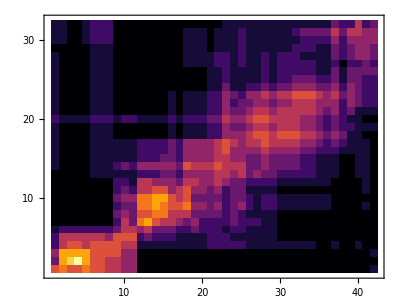

```mathematica
With[{i=60},
mknnPlot[Outer[Length@*Intersection,knn1[[All,i]],knn2[[All,i]],1]/10]
]
```

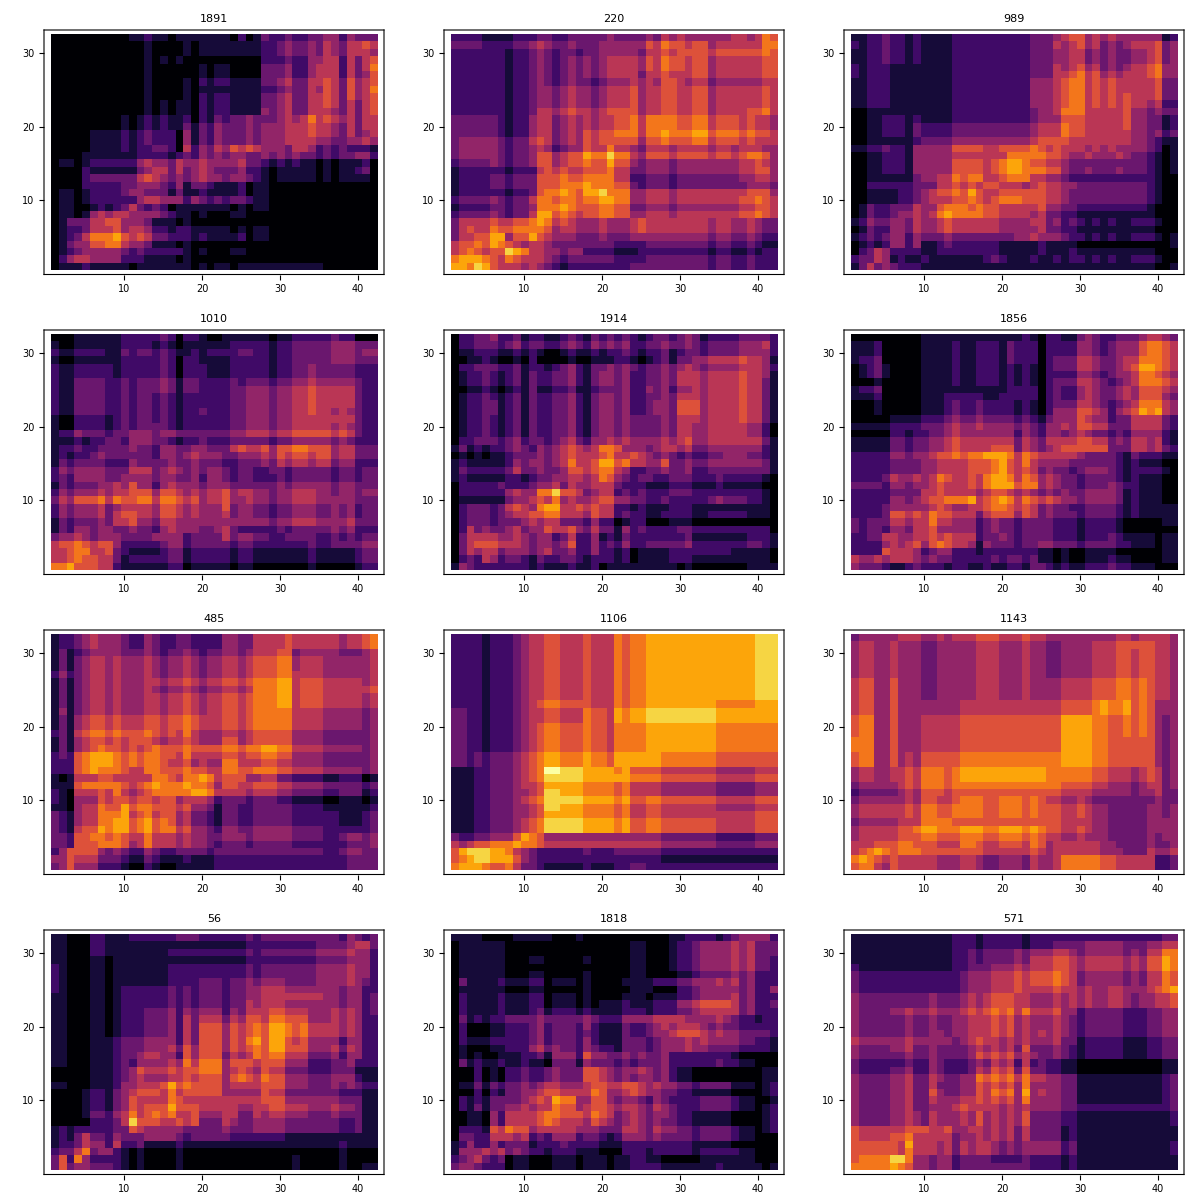

```mathematica
Multicolumn[
mknnPlot[
Outer[Length@*Intersection,knn1[[All,#]],knn2[[All,#]],1]/10,
PlotLegends->None,
PlotLabel->#
]&/@RandomSample[Range[2048],12],
3
]
```

### 3D plots

```mathematica
computeMKNN[knns___]:=Mean[N@MapThread[Length@*Intersection,{knns}]]/Length[{knns}[[1]]]
```

```mathematica
knn1=getKNN[{"google/gemma-2-9b","web_text"}];
knn2=getKNN[{"meta-llama/Meta-Llama-3.1-8B","web_text"}];
knn3=getKNN[{"mistralai/Mistral-7B-v0.3","web_text"}];
```

```mathematica
mknn3D=Table[computeMKNN[a,b,c],{a,knn1},{b,knn2},{c,knn3}];//EchoTiming
```

99.1685

```mathematica
mknn3D=;
```

```mathematica
MinMax[mknn3D]
```

{0.000254154,0.00218868}

```mathematica
ListDensityPlot3D[mknn3D]
```

-Graphics3D-

### Distance scatter plot

```mathematica
mknnPlot@lookupMKNN[allMKNN["web_text"],{"meta-llama/Meta-Llama-3.1-8B","google/gemma-2-9b"}]
```

```mathematica
mknnPlot@lookupMKNN[allMKNN["web_text"],{"meta-llama/Meta-Llama-3.1-8B","google/gemma-2-9b"}]
```

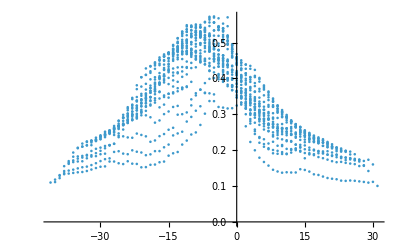

```mathematica
ListPlot@Catenate@MapIndexed[
{Subtract@@#2,#1}&,
lookupMKNN[allMKNN["web_text"],{"meta-llama/Meta-Llama-3.1-8B","google/gemma-2-9b"}],
{2}
]
```

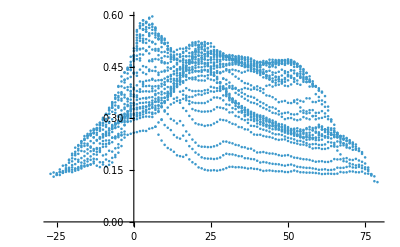

```mathematica
ListPlot@Catenate@MapIndexed[
{Subtract@@#2,#1}&,
lookupMKNN[allMKNN["web_text"],{"meta-llama/Llama-3.1-70B","meta-llama/Llama-3.2-3B"}],
{2}
]
```

```mathematica
mknnPlot@lookupMKNN[allMKNN["web_text"],{"meta-llama/Llama-3.1-70B","meta-llama/Llama-3.1-70B"}]
```

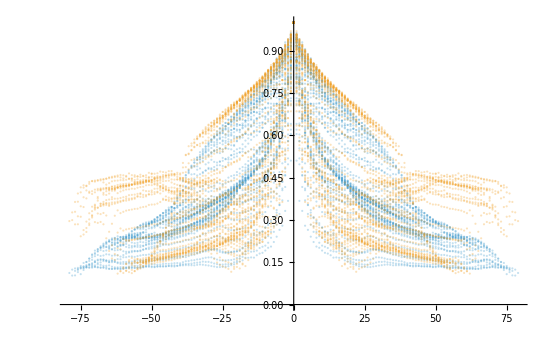

```mathematica
ListPlot[{
Catenate@MapIndexed[
{Subtract@@#2,#1}&,
lookupMKNN[allMKNN["web_text"],{"meta-llama/Llama-3.1-70B","meta-llama/Llama-3.1-70B"}],
{2}
],
Catenate@MapIndexed[
{Subtract@@#2,#1}&,
lookupMKNN[allMKNN["random_strings"],{"meta-llama/Llama-3.1-70B","meta-llama/Llama-3.1-70B"}],
{2}
]
},
PlotStyle->Opacity[0.3]
]
```